# Lab: Modeling Chemical Kinetics

## Introduction

In chemical kinetics, we care about the rate of a reaction.  Specifically, we care about how the concentration of one or more reactants (and/or products) changes over some period of time.  Mathematically, we use differential equations to solve these types of problems.

As an example, suppose we have some reactant A changing to become B.  This reaction happens at some reaction rate k, shown above the reaction arrow.  In the laboratory, we have determined that this reaction is a first order reaction.   Since there is only one reactant, the reaction is first order in A and first order overall.

A→^k B

Mathematically, we care about how the concentration of A -- represented as [A] -- changes over time.  We

Δ[A]/Δt= -k[A]
Δ[B]/Δt= k[A]

Typically, mostly for ease of typesetting, we use the letter "d" instead of "Δ", so the notation looks like this:

d[A]/dt= -k[A]
d[B]/dt= k[A]

One important characteristic of these two differential equations:  notice that the mathematics on the right side of the first equation is the same as the mathematics on the right side of the second equation, with the exception of the minus sign.  This means that these equations are coupled differential equations.  This characteristic will prove to be very helpful when you do the lab, and you should look for equations that are coupled.  

The value "k" is the rate constant for this particular reaction.  The rate constant can only be determined experimentally, and you have some experience with that.  Likewise, the kinetics shown above is first order in A, and first order overall.  This too can only be determined experimentally. 

To solve these equations, we need to use integral calculus.  Suppose we want to run this reaction for 15 minutes.  If that is the case, the calculus would look like this:

Δ[A] = -k∫_0^15 [A]ⅆt
Δ[B] = k∫_0^15 [B]ⅆt

The solution of these integrals starts with an initial value for [A] and [B], meaning the concentration of these chemicals at the beginning of the reaction (when time = 0, or t = 0).  We designate these initial concentrations as [A]_0 (and [B])_0.  Lower-case symbols, such as k, typically are used to indicate constants.

More complicated reactions are typically shown as a reaction mechanism, a series of steps that describe the overall reaction.  As a part of this lab activity, you will be asked to model an oscillating reaction using the Lotka-Volterra mechanism:

d[X]/dt= k_1[A]-k_2[X][Y]
d[Y]/dt= k_2[X][Y]-k_3[Z]
d[Z]/dt= k_3[Z]

```mathematica
Clear["Global`*"]
```

## Models

### Model 1: Simple First Order Kinetics

Build a simple first order kinetics model shown in Equation 1 (and represented mathematically in Equation 3).  For this model, use these parameters:

[A]_0 = 2 {moles}

[B]_0 = 0 {moles}

k = 0.5  min^-1

```mathematica
k = 0.5;
```

```mathematica
solution = NDSolve[
{
a'[t] == -k a[t],
b'[t] == k a[t],
a[0] == 2,
b[0] ==0
},
{a, b},
{t, 0, 30},
MaxSteps-> Infinity
]
```

{{a→InterpolatingFunction[…],b→InterpolatingFunction[…]}}

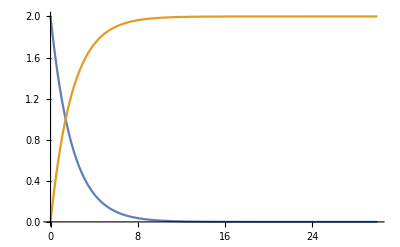

```mathematica
Plot[Evaluate[{a[t], b[t]} /. solution], {t, 0, 30},PlotRange->All]
```

### Model 2: Parallel First Order Kinetics

A→^k_1 B
A→^k_2 C

d[A]/dt= -k_1[A]- k_2[A]
d[B]/dt= k_1[A]                  
d[C]/dt= k_2[A]

Build a simple first order kinetics model shown in Equation 6 (and represented mathematically in Equation 7).  For this model, use these parameters:

[A]_0 = 2 {moles}

[B]_0 =0 {moles}

[C]_0 =0 {moles}

k_1 = 0.5  min^-1

k_2 = 1 min^-1

```mathematica
k1 = 0.5;
k2 = 1;
```

```mathematica
parallel = NDSolve[
{
a'[t] == -k1 a[t] - k2 a[t],
b'[t] == k1 a[t],
c'[t] == k2 a[t],
a[0] == 2,
b[0]== 0,
c[0] == 0
},
{a, b, c},
{t,0, 30},
MaxSteps->Infinity
]
```

{{a→InterpolatingFunction[…],b→InterpolatingFunction[…],c→InterpolatingFunction[…]}}

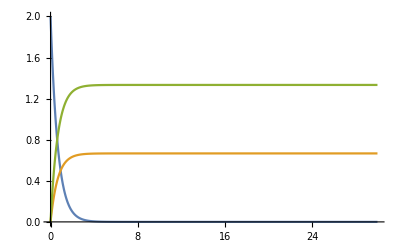

```mathematica
Plot[Evaluate[{a[t], b[t], c[t]} /. parallel], {t, 0, 30},PlotRange->All]
```

### Model 3: Consecutive First Order Kinetics

A→^k_1 B→^k_2 C

d[A]/dt= -k_1[A]
d[B]/dt= k_1[A]- k_2[B]                  
d[C]/dt= k_2[B]

Build a simple first order kinetics model shown in Equation 8 (and represented mathematically in Equation 9).  For this model, use these parameters:

[A]_0 = 2 {moles}

[B]_0 =0 {moles}

[C]_0 =1e-5 {moles}

k_1 = 0.5 min^-1

k_2 = 1 min^-1

```mathematica
k1 = 0.5;
k2 = 0.5;
```

```mathematica
consecutive = NDSolve[
{
a'[t] == -k1 a[t],
b'[t] == k1 a[t] - k2 b[t],
c'[t] == k2 b[t],
a[0] == 2,
b[0]== 0,
c[0] == 1 ^-3
},
{a, b, c},
{t,0, 30},
MaxSteps->Infinity
]
```

{{a→InterpolatingFunction[…],b→InterpolatingFunction[…],c→InterpolatingFunction[…]}}

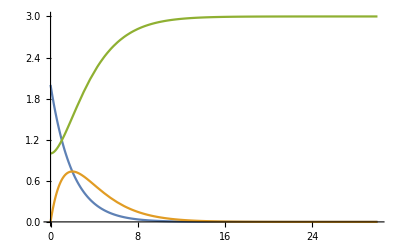

```mathematica
Plot[Evaluate[{a[t], b[t], c[t]} /. consecutive], {t, 0, 30},PlotRange->All]
```

### Model 4: Reversible First Order Kinetics

A(⇌^k_1)_(k_-1)B(⇌^k_2)_(k_-2)C

d[A]/dt= -k_1[A]+k_-1[B]
d[B]/dt= k_1[A]- k_2[B]+k_-2[C]- k_-1[B]       
d[C]/dt= k_2[B]-  k_-2[C]

Build a simple first order kinetics model shown in Equation 10 (and represented mathematically in Equation 11).  For this model, use these parameters:

[A]_0 = 2 {moles}

[B]_0 =0 {moles}

[C]_0 =0 {moles}

k_1 = k_2 = k_-1 = k_-2= 0.5 min^-1

```mathematica
k1 = 0.5;
k2 = 0.5;
k3 = 0.5;
k4 = 0.5;
```

```mathematica
reversible = NDSolve[
{
a'[t] == -k3 a[t] + -k3 b[t],
b'[t] == k1 a[t] - k2 b[t] + k4 c[t] - k3 b[t],
c'[t] == k3 b[t] - k4 c[t],
a[0] == 2,
b[0]== 0,
c[0] == 0
},
{a, b, c},
{t,0, 30},
MaxSteps->Infinity
]
```

{{a→InterpolatingFunction[…],b→InterpolatingFunction[…],c→InterpolatingFunction[…]}}

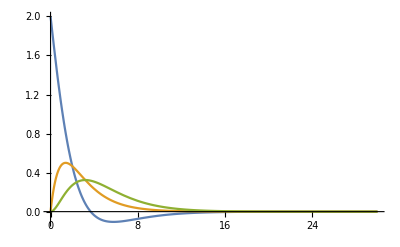

```mathematica
Plot[Evaluate[{a[t], b[t], c[t]} /. reversible], {t, 0, 30},PlotRange->All]
```

### Mini-Project: Modeling the Lotka-Volterra Kinetics Mechanism

One of the more important models in chemical kinetics (and in the study of biological systems, such as predator-prey interactions) is the Lotka-Volterra mechanism.  This mechanism is in a category of reactions known as oscillating reactions.  You saw a simple example in the bromine-iodine clock reaction lab.  

The mechanism shown in Equation 13 is the mathematics for the damped Lotka-Volterra oscillating reaction mechanism.

d[X]/dt= k_1[W]-k_2[X][Y]
d[Y]/dt= k_2[X][Y]-k_3[Y]
d[Z]/dt= k_3[Y]

#### Part A: Damped Model

Build the damped Lotka kinetics model shown in Equation 12.  For this model, use these parameters:

[W] = 0.5 {moles}.  NOTE!  This represents a starting amount of a reactant that is acts as a "starter" for the reaction.  In essence, you have an unlimited amount of "W" in this reaction.  As soon as some of reactant W is used in the reaction, more W is provided from an external source.  In other words, the beaker holding W is constantly being refilled!

[X]_0 =0.1 {moles}

[Y]_0 =0.01 {moles}

[Z]_0 =0 {moles}

k_1 = 0.3 min^-1

k_2 = 0.6 min^-1

k_3 = 0.4 min^-1

```mathematica
w = 0.5;
k1 = 0.3;
k2 = 0.6;
k3 = 0.4;
```

```mathematica
damped = NDSolve[
{
x'[t] == k1 w - k2 x[t] y[t],
y'[t] == k2 x[t] y[t] - k3 y[t],
z'[t] == k3 y[t],
x[0] == 0.1,
y[0] == 0.01,
z[0] == 0
},
{x, y, z},
{t, 0, 30},
MaxSteps->Infinity
]
```

{{x→InterpolatingFunction[…],y→InterpolatingFunction[…],z→InterpolatingFunction[…]}}

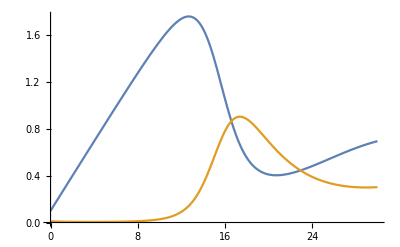

```mathematica
Plot[Evaluate[{x[t], y[t]} /. damped], {t, 0, 30},PlotRange->All]
```

#### Part B: Undamped (Oscillating) Model

d[X]/dt= k_1[W][X]-k_2[X][Y]
d[Y]/dt= k_2[X][Y]-k_3[Y]
d[Z]/dt= k_3[Y]

Build the undamped Lotka kinetics model shown in Equation 13.  See if you can find the very subtle difference in the damped model version the undamped model.  For this model, use these parameters:

[W] = 0.5 {moles}.

[X]_0 =0.1 {moles}

[Y]_0 =0.01 {moles}

[Z]_0 =0 {moles}

k_1 = 0.3 min^-1

k_2 = 0.6 min^-1

k_3 = 0.4 min^-1

```mathematica
w = 0.5;
k1 = 0.3;
k2 = 0.6;
k3 = 0.4;
```

```mathematica
undamped = NDSolve[
{
x'[t] == k1 w k2 x[t]- k2 x[t] y[t],
y'[t] == k2 x[t] y[t] - k3 y[t],
z'[t] == k3 y[t],
x[0] == 0.1,
y[0] == 0.01,
z[0] == 0
},
{x, y, z},
{t, 0, 30},
MaxSteps->Infinity
]
```

{{x→InterpolatingFunction[…],y→InterpolatingFunction[…],z→InterpolatingFunction[…]}}

```mathematica
Plot[Evaluate[{x[t], y[t]} /. damped], {t, 0, 30},PlotRange->All]
```

-Graphics-